## Initializing

#### Candidate ranges

from findcriticaleigenvalues (other notebook). Found with ρinf = 20*λ. First three λcs sort of added in there.

```mathematica
ranges={{0.5,1.},{3.,4.},{6.5,7.5},{12.900390625,13.8671875},{19.66796875,20.634765625},{28.369140625,29.3359375},{39.00390625,39.970703125},{50.60546875,51.572265625},{64.140625,65.107421875},{78.642578125,79.609375},{96.044921875,97.01171875},{113.447265625,114.4140625},{133.75,134.716796875},{155.01953125,155.986328125},{178.22265625,179.189453125},{202.392578125,203.359375},{228.49609375,229.462890625},{255.56640625,256.533203125},{285.537109375,286.50390625},{315.5078125,316.474609375},{348.37890625,349.345703125},{382.216796875,383.18359375},{417.98828125,418.955078125},{454.7265625,455.693359375},{493.3984375,494.365234375},{533.037109375,534.00390625},{574.609375,575.576171875},{618.115234375,619.08203125},{663.5546875,664.521484375},{709.9609375,710.927734375},{757.333984375,758.30078125},{807.607421875,808.57421875},{858.84765625,859.814453125},{911.0546875,912.021484375},{965.1953125,966.162109375}};
```

#### Functions for finding λcs

This function pulls out the list of the 25 eigenvalues closest to zero. Around the lower lambdas, that is rough for bisection.

```mathematica
Critical[λ_,consts_]:=Module[{H,res,dρ,ρinf,nn},
dρ=consts[[1]];
ρinf=consts[[2]];
nn=consts[[3]];
H=SparseArray[{{n_,n_}->2./dρ^2-2./(n*dρ)ⅇ^(-n*dρ/λ),{n_, m_}/; Abs[n-m] == 1 -> -1./dρ^2},{nn,nn}, 0.];
res=Sort[Eigenvalues[H,-25]];(*Went from 100 down to 25 eigenvalues, which sped this calculation up immensely with no apparent loss of information*)
Return[res]
]
```

This one counts the negative eigenvalues at some λ.

```mathematica
CountNegs[list_]:=Module[{neg,i},
neg=0;
For[i=1,list[[i]]<0,i++,
neg++;
];
Return[neg]
]
```

This is a bisection routine. It tries to catch when eigenvalues fall off the end by checking to see whether the first eigenvalue at the high end of the range is lower than the first eigenvalue at the low end of the range. This usually means that one was lost.

```mathematica
Bisect[F_,consts_,x0_,xf_,ϵ_]:=Module[{mid,val,lnegs,vam,mnegs,ret},
mid=x0+Abs[x0-xf]/2;
Print["Bisecting. Midpoint is "<>ToString[mid]];
val=F[x0,consts];
lnegs=CountNegs[val];
vam=F[mid,consts];
mnegs=CountNegs[vam];
If[xf-x0>ϵ,
(*Print[{lnegs,mnegs},{val[[1]],vam[[1]]}];*)
If[lnegs<mnegs || (lnegs==mnegs && val[[1]] < vam[[1]]),
Return[Bisect[F,consts,x0,mid,ϵ]];,
Return[Bisect[F,consts,mid,xf,ϵ]];
];,
Return[mid];
]
]
```

This function finds the lambda critical. I use this because I wanted to make sure I was bisecting a range with a root in it.

```mathematica
Findlc[input_,i_]:=Module[{val,vah,lnegs,hnegs,res},
Print["***Beginning to calculate the "<>ToString[Ceiling[i,3]/3]<>"th lambda, part "<>ToString[input[[1]]]];
val=Critical[input[[3]],{0.1,input[[2]],input[[2]]/0.1}];
vah=Critical[input[[4]],{0.1,input[[2]],input[[2]]/0.1}];
lnegs=CountNegs[val];
hnegs=CountNegs[vah];
If[lnegs<hnegs || (lnegs==hnegs && val[[1]]<vah[[1]]),(*doublechecks for zero*)
Print["Pass!"];
res={input[[1]],Bisect[Critical,{0.1,input[[2]],input[[2]]/0.1},input[[3]],input[[4]],10^(-6)]};
,(*else*)
Print["Fail!"];
res={input[[1]],Null};
];
Print[{{val[[1]],lnegs},{vah[[1]],hnegs}}];
Return[res]
]
```

This will be needed later, for folding in recomputed values in the event of a range without a zero.

```mathematica
Merge[a_,b_]:=Module[{vals,res},
res=a;
vals=b;
For[i=1,i≤Length[res],i++,
If[res[[i,2]]==Null,(*if this was a recomputed value*)
res[[i]]=vals[[1]]; (*Slot in the head of the list of recomputed values*)
vals=Delete[vals,1]; (*and delete it, moving the next value to the head*)
];
];
Return[res]
]
```

#### Massaging inputs:

```mathematica
rhoinfs={80*1000.,160*1000.};
```

Making a list of inputs -- {number, ρinf, range low, range high}. Joins done in order to broaden some ranges.

```mathematica
inputs=Join[{Table[{j,rhoinfs[[j]],ranges[[1,1]],ranges[[1,2]]},{j,1,2}]},Table[Table[{j,rhoinfs[[j]],ranges[[i,1]]-1,ranges[[i,2]]+1},{j,1,2}],{i,2,Length[ranges]}]];
```

```mathematica
inputs = Flatten[inputs, 1]
```

{{1,80000.,0.5,1.},{2,160000.,0.5,1.},{1,80000.,2.,5.},{2,160000.,2.,5.},{1,80000.,5.5,8.5},{2,160000.,5.5,8.5},{1,80000.,11.9004,14.8672},{2,160000.,11.9004,14.8672},{1,80000.,18.668,21.6348},{2,160000.,18.668,21.6348},{1,80000.,27.3691,30.3359},{2,160000.,27.3691,30.3359},{1,80000.,38.0039,40.9707},{2,160000.,38.0039,40.9707},{1,80000.,49.6055,52.5723},{2,160000.,49.6055,52.5723},{1,80000.,63.1406,66.1074},{2,160000.,63.1406,66.1074},{1,80000.,77.6426,80.6094},{2,160000.,77.6426,80.6094},{1,80000.,95.0449,98.0117},{2,160000.,95.0449,98.0117},{1,80000.,112.447,115.414},{2,160000.,112.447,115.414},{1,80000.,132.75,135.717},{2,160000.,132.75,135.717},{1,80000.,154.02,156.986},{2,160000.,154.02,156.986},{1,80000.,177.223,180.189},{2,160000.,177.223,180.189},{1,80000.,201.393,204.359},{2,160000.,201.393,204.359},{1,80000.,227.496,230.463},{2,160000.,227.496,230.463},{1,80000.,254.566,257.533},{2,160000.,254.566,257.533},{1,80000.,284.537,287.504},{2,160000.,284.537,287.504},{1,80000.,314.508,317.475},{2,160000.,314.508,317.475},{1,80000.,347.379,350.346},{2,160000.,347.379,350.346},{1,80000.,381.217,384.184},{2,160000.,381.217,384.184},{1,80000.,416.988,419.955},{2,160000.,416.988,419.955},{1,80000.,453.727,456.693},{2,160000.,453.727,456.693},{1,80000.,492.398,495.365},{2,160000.,492.398,495.365},{1,80000.,532.037,535.004},{2,160000.,532.037,535.004},{1,80000.,573.609,576.576},{2,160000.,573.609,576.576},{1,80000.,617.115,620.082},{2,160000.,617.115,620.082},{1,80000.,662.555,665.521},{2,160000.,662.555,665.521},{1,80000.,708.961,711.928},{2,160000.,708.961,711.928},{1,80000.,756.334,759.301},{2,160000.,756.334,759.301},{1,80000.,806.607,809.574},{2,160000.,806.607,809.574},{1,80000.,857.848,860.814},{2,160000.,857.848,860.814},{1,80000.,910.055,913.021},{2,160000.,910.055,913.021},{1,80000.,964.195,967.162},{2,160000.,964.195,967.162}}

## Computation -- TAKES A LONG TIME

```mathematica
len=Length[inputs]
```

70

First, distribute:

```mathematica
DistributeDefinitions[Findlc,Bisect,Critical,CountNegs,inputs,len]
```

Then compute! This is a total of seven computations per core, each of which is 23 bisections. Each bisection calls Critical[] twice and takes roughly 0.11 hours (six minutes, give or take) for the higher value of rhoinf. This means the entire calculation should run in about 14 hours.

```mathematica
lcs=ParallelTable[Findlc[inputs[[i]],i],{i,1,len}]
```

Find all the ones which were missed and then expand their ranges.

```mathematica
missed={};
For[i=1,i≤Length[lcs],i++,
If[lcs[[i,2]]==Null,
missed=Append[missed,i]
]
]
```

This creates a table with only the inputs where an eigenvalue was not found in the range.

```mathematica
newins=Table[{inputs[[missed[[i]],1]],inputs[[missed[[i]],2]],inputs[[missed[[i]],3]]-1,inputs[[missed[[i]],4]]+1},{i,1,Length[missed]}];
```

We then rerun the computation with those inputs:

```mathematica
DistributeDefinitions[newins]
```

```mathematica
missedlcs=ParallelTable[Findlc[inputs[[i]],i],{i,1,Length[newins]}]
```

```mathematica
lcs=Merge[lcs,missedlcs]
```

Loop as necessary. Looping should be manual, at least for now.

## Analysis and Fit

Table with data in the form {λc, err}

```mathematica
data=Table[{lcs[[i,2]],lcs[[i,2]]-lcs[[i+1,2]]},{i,1,Length[lcs],2}];
```

### Graphs!

```mathematica
Needs["ErrorBarPlots`"];
```

```mathematica
graph= ErrorBarPlots`ErrorListPlot[data]
```

```mathematica
loglog=Table[{Log[N[i]],Log[data[[i,1]]],1/data[[i,1]]*data[[i,2]]},{i,1,Length[data]}];
```

```mathematica
ListPlot[Table[{loglog[[i,1]],loglog[[i,2]]},{i,1,Length[loglog]}]]
```

### Fit

Using w_i = 1/Δi^2, from Taylor.

```mathematica
weights=Table[1/(loglog[[i,3]]^2),{i,1,Length[loglog]}];
```

This is also from Taylor, used below

```mathematica
Delta=Sum[weights[[i]],{i,Length[weights]}]*Sum[weights[[i]]*loglog[[i,1]]^2,{i,Length[loglog]}]-(Sum[weights[[i]]*loglog[[i,1]],{i,Length[loglog]}])^2;
```

More symbols to make expressions less unweildy.

```mathematica
x[i_]:=loglog[[i,1]];
y[i_]:=loglog[[i,2]];
w[i_]:=weights[[i]];
```

Now, the fit coefficients (for line off form y = A + Bx):

```mathematica
A=1/Delta(Sum[w[i]*x[i]^2,{i,Length[data]}]*Sum[w[i]*y[i],{i,Length[data]}]-Sum[w[i]*x[i],{i,Length[data]}]*Sum[w[i]*x[i]*y[i],{i,Length[data]}])
```

-0.225343

```mathematica
B=1/Delta(Sum[w[i],{i,Length[data]}]*Sum[w[i]*x[i]*y[i],{i,Length[data]}]-Sum[w[i]*x[i],{i,Length[data]}]*Sum[w[i]*y[i],{i,Length[data]}])
```

1.99456

Again, not quite quadratic. We can plot both:

```mathematica
F[x_]:=A+B*x
```

```mathematica
Needs["ErrorBarPlots`"]
```

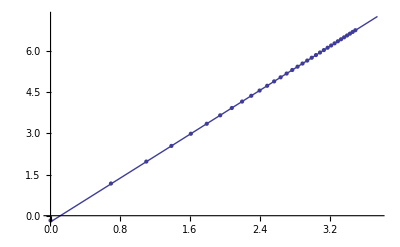

```mathematica
Show[Plot[F[x],{x,0,3.75}],ErrorListPlot[Table[{{x[i],y[i]},ErrorBar[loglog[[i,3]]]},{i,1,34}]]]
```

Uncertainties in A and B:

```mathematica
σA=Sqrt[Sum[w[i]*x[i]^2,{i,14}]/Delta]
```

0.0000517341

```mathematica
σB=Sqrt[Sum[w[i],{i,14}]/Delta]
```

0.0000282434

Checking the goodness of the fit:

```mathematica
fitvals=Table[F[loglog[[i,1]]],{i,1,33}];
```

```mathematica
residuals=Table[fitvals[[i]]-loglog[[i,2]],{i,1,33}];
```

This expression should output a list of booleans. TRUE means that the fit is inside the error bars (resdiual < error bar) and FALSE means it’s outside

```mathematica
Table[Abs[residuals[[i]]]<loglog[[i,3]],{i,1,33}]
```

{False,False,False,False,False,False,False,False,False,False,False,False,False,True,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False,False}